```mathematica
fX[x_]:=3*x^2*Exp[-x^3/theta^3]/theta^3
delta[x_,t_]:= Pi*((c0*t+x)^2-(c1*t)^2)

Integrate[delta[x,t],{t,0,x/(c1-c0)}]
```

(c0 π x^3)/(c0-c1)^2+(c0^2 π x^3)/(3 (-c0+c1)^3)-(c1^2 π x^3)/(3 (-c0+c1)^3)+(π x^3)/(-c0+c1)

```mathematica
Integrate[Exp[-rho*mu*((c0 π x^3)/(c0-c1)^2+(c0^2 π x^3)/(3 (-c0+c1)^3)-(c1^2 π x^3)/(3 (-c0+c1)^3)+(π x^3)/(-c0+c1))]*fX[x],{x,0,Infinity}]
```

ConditionalExpression[(3 (c0-c1)^2)/(3 (c0-c1)^2-(c0-2 c1) mu π rho theta^3), ]

```mathematica
theta3=3*c0/(Pi*rho*mu)
```

(3 c0)/(mu π rho)

```mathematica
(3 (c0-c1)^2)/(3 (c0-c1)^2-(c0-2 c1) mu π rho theta3)
```

(3 (c0-c1)^2)/(-3 c0 (c0-2 c1)+3 (c0-c1)^2)

```mathematica
c0=1
```

1

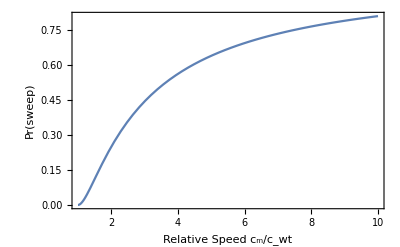

```mathematica
Plot[(3 (c0-c1)^2)/(-3 c0 (c0-2 c1)+3 (c0-c1)^2),{c1,1,10},Frame->True,FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True]
```